# Linguistic Universal

### Intro

Linguistic universals are the features shared across languages.  They help us understand the similarities and differences between the way we pass & store information. Studying them may potentially help us understand the processes of cognition and perception. What are some simple examples of those features?

All languages seem to have nouns and verbs.

All spoken languages seem to have consonants and vowels.

Most languages have pronouns.

They are generally divided into 2 categories: absolute & implicational. 
The first one contains features shared between all the languages, while the second has features that appear just within a subset of them.

### Terminology

Morpheme is the smallest unit of form and meaning. It arises naturally in the analysis of every language.

Word is trickier to define. There are at least two troublesome issues:

making the distinction between words and phrases, and

the status of certain grammatical formatives known as clitics.

Morphology is the study of words, how they are formed, and their relationship to other words in the same language.

Typology is a field of linguistics that studies and classifies languages according to their structural and functional features.

Phonology is a branch of linguistics concerned with the systematic organization of sounds in spoken languages and signs in sign languages.

Syntax is the set of rules, principles, and processes that govern the structure of sentences (sentence structure) in a given language, usually including word order.

Semantics is the linguistic and philosophical study of meaning in language. Branch of this is “lexical semantics”.

### Shared Code & Data

```mathematica
DrawSimilaritiesGraph[vertexNames_List, edgesWeights2D_List] := Module[{g, gp, edgeAssoc},
	g = WeightedAdjacencyGraph[vertexNames, edgesWeights2D, DirectedEdges -> False, VertexLabels -> "Name", GraphLayout -> "CircularEmbedding"];
	edgeAssoc = AssociationThread[EdgeList[g] -> AbsoluteOptions[g, EdgeWeight]⟦1,2⟧];
	gp = GraphPlot[g, EdgeStyle -> Normal[Directive[Thickness[0.01], Hue[#], Opacity[#]] & /@ edgeAssoc]];
	gp
];
RemoveDiagonalElements[edgesWeights2D_List] := edgesWeights2D - DiagonalMatrix[Diagonal[edgesWeights2D]];
BuildAdjacencyMatrix[func_, matrixSide_Integer] := Table[func[i, j], {i, matrixSide}, {j, matrixSide}] // RemoveDiagonalElements // MatrixForm // First // Rescale;
BuildAdjacencyMatrix[func_, rowNames_List] := BuildAdjacencyMatrix[func, Length[rowNames]];
WordsIn[langName_] := Normal @ Take[WordList[Language -> langName] // ToLowerCase // RemoveDiacritics, UpTo[10000]];
```

```mathematica
dataSwadesh = ResourceData["Swadesh Lists"];
langsAll = Normal @ Take[Keys[dataSwadesh], UpTo[8]];
langsPrimary = {
	"English", "German", "French", "Italian", "Polish", "Hungarian", 
	"Catalan", "Spanish", "Portuguese", (* "BrazilianPortuguese", *)
	"Danish", "Swedish", "Finnish", "Dutch", "IrishGaelic", "ScottishGaelic" 
};
```

### Swadesh Corpora

One of the best-known works in this field is the “Greenbergs universals” list with over 30 different features shared across languages. It primarily covers structural patterns present in most of the known languages. Those properties are hard to define and even harder to study using statistical methods. Lexical similarities, on the other hand, are a natural entry point for universals analysis. Most common modern languages today have very similar corpora, but often words in one language don’t have a fully matching translation in the other language:

```mathematica
Grid[{
	{"Russian", "English"}, 
	{"голубой", First @ WordTranslation["голубой", "Russian" -> "English"]}, 
	{ "синий", First @ WordTranslation["синий", "Russian" -> "English"] }}, 
Frame -> {1, True, False}, Dividers -> {False, 2 -> True}]
```

Russian | English
голубой | blue
синий | blue

The Swadesh corpora was constructed specially for that purpose. It originally defined 100 popular & common words in 30 languages, but was later extended to □Length[Keys[ResourceData["Swadesh Lists"]]] languages. Let's see how close are they to each other?

```mathematica
(* Utilitary functions *)
WordsTranslatedTo[targetLangIdx_Integer] := Normal @  Keys[Query[langsAll⟦targetLangIdx⟧] @ dataSwadesh];
WordsTranslatedToBoth[targetLangAIdx_Integer, targetLangBIdx_Integer] := Normal @ Take[Intersection[WordsTranslatedTo[targetLangAIdx], WordsTranslatedTo[targetLangBIdx]], UpTo[50]];
WordsTranslateTo[wordsInEng_List, targetLangIdx_Integer] := Normal @  Values[Query[targetLangIdx, wordsInEng] @ dataSwadesh];
WordsLimit[wordsInLang_List] := (Take[#, UpTo[3]]) & /@ wordsInLang; (* If language A has NA translations for word X and language B has NB translations, then it will take us (NA*NB) expensive operations to compute distances. Instead we should limit the number of variants. *)
WordsNormalize[wordsInLang_List] := (StringDelete[#, Except[WordCharacter]]) & /@ ToLowerCase /@ RemoveDiacritics /@ Transliterate /@ wordsInLang;

(* The similarity metrics *)
WordsDissimilarity[wordA_String, wordB_String] := DamerauLevenshteinDistance[wordA, wordB] / Max[StringLength[wordA], StringLength[wordB]];
WordsDissimilarity[wordA_List, wordB_List] := WordsDissimilarity[wordA⟦1⟧, wordB⟦1⟧];
WordsPairDissimilarity[wordsPair_] := WordsDissimilarity[wordsPair⟦1⟧, wordsPair⟦2⟧];
WordsSetsDissimilarity[wordsA_List, wordsB_List] := Min[Map[WordsPairDissimilarity, Tuples[{wordsA, wordsB}]]];
LanguagesSimilarity[langIdxA_Integer, langIdxB_Integer] := Module[{sharedInEng, translatedToA, translatedToB, distancesPerTranslatin},
	(* First we need to extract words that were translated to both languages. *)
	sharedInEng = WordsTranslatedToBoth[langIdxA, langIdxB];
	(* Then we need to translate those 2 separately and find how close *)
	translatedToA = WordsNormalize @ WordsLimit@ WordsTranslateTo[sharedInEng, langIdxA];
	translatedToB = WordsNormalize @ WordsLimit@ WordsTranslateTo[sharedInEng, langIdxB];
	If[Length[translatedToA] ≠ Length[translatedToB], Throw[Null, "Not all translations found!"]];
	distancesPerTranslatin = MapThread[WordsSetsDissimilarity, {translatedToA,translatedToB}];
	1 - Mean[distancesPerTranslatin]
];
```

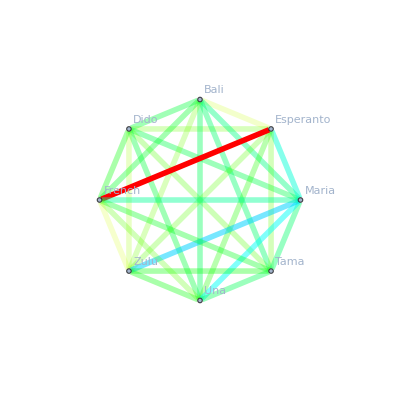

```mathematica
DrawSimilaritiesGraph[langsAll, BuildAdjacencyMatrix[LanguagesSimilarity, langsAll]]
```

In origin, the words in the Swadesh lists were chosen for their universal, culturally independent availability in as many languages as possible, regardless of their “stability”. Nevertheless, the stability of the resulting list of “universal” vocabulary under language change and the potential use of this fact for purposes of glottochronology have been analyzed by numerous authors, including Marisa Lohr (1999, 2000). The Swadesh list was put together by Morris Swadesh on the basis of his intuitions. More recent alternatives are:

the Dolgopolsky list (1964) or

the Leipzig–Jakarta list (2009),

are based on systematic data from many different languages, but they are not yet as widely known nor as widely used as the Swadesh list.

### Full European Lexicon

To be able to compare languages coming not just from a different region in space, but also from different periods in time, we had to give up some of the information encoded into the structure of each word. Nowadays our languages often use the same writing system & alphabet derived from Latin, so similarities are much easier to trace. So the next logical step to make the statistics more representative is to analyze modern European languages.

```mathematica
(* 1. Constants and Variables *)
wordsPerLang = Map[WordsIn, langsPrimary];
wordsCountsPerLang = Map[Length, wordsPerLang];

(* 2. Cache Parsed Data *)
WordsPresentInBoth[langWordsA_, langWordsB_] := Length[Intersection[langWordsA, langWordsB]];
WordsPresentInBoth[langIdxA_Integer, langIdxB_Integer] := WordsPresentInBoth[wordsPerLang⟦langIdxA⟧, wordsPerLang⟦langIdxB⟧];
```

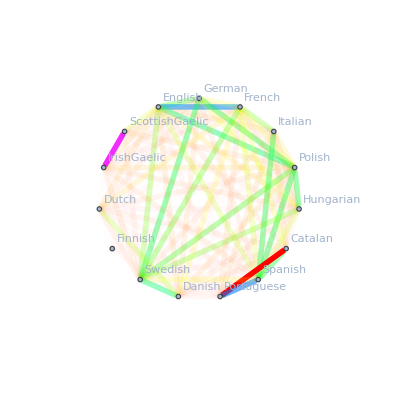

```mathematica
DrawSimilaritiesGraph[langsPrimary, BuildAdjacencyMatrix[WordsPresentInBoth, langsPrimary]]
```

This graph lets us visually quantify some of the well known facts about the European languages.

Finish is a very distinct languages, which is not as close to Swedish, as many tend to think.

Even though Catalan is spoken in North-Eastern part of Spain, the region is culturally very different from the rest of the country. Even their language is closer to Portuguese, then to Spanish.

Gaelic languages are very similar and even though Scotland and Ireland are separated by a huge water body, given the naval nature of their cultures, they are closer to each other, then to England.